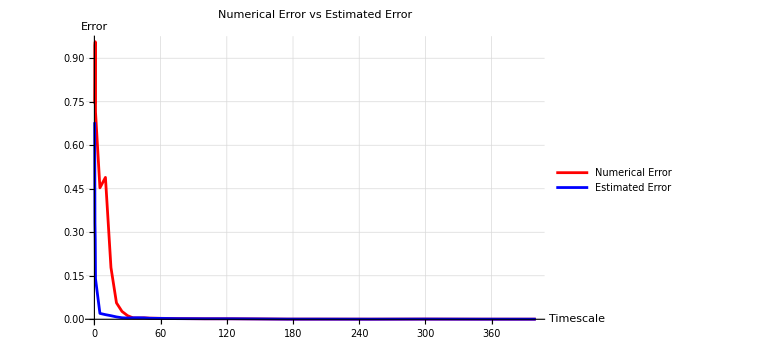

```mathematica
data={{0.25,0.743221,0.679376},{0.5,0.944702,0.33125},{0.75,0.956842,0.275258},{1,0.714626,0.139382},{5,0.453195,0.0202892},{10,0.489112,0.0159122},{15,0.178445,0.0123229},{20,0.0564877,0.0081473},{25,0.02709,0.00524032},{30,0.0125538,0.00430966},{35,0.00476088,0.00509585},{40,0.00420211,0.00530321},{45,0.00492376,0.00477037},{50,0.00393889,0.00352544},{75,0.00238335,0.00219435},{100,0.00174119,0.00178187},{125,0.00167612,0.00171166},{150,0.0011642,0.00116305},{175,0.000549537,0.000586142},{200,0.000569245,0.000599354},{250,0.000439756,0.00041137},{300,0.000697584,0.000696216},{350,0.000439762,0.00044649},{400,0.000385479,0.000385278}};

timescale=data[[All,1]];
numericalError=data[[All,2]];
estimatedError=data[[All,3]];

ListLinePlot[{Transpose[{timescale,numericalError}],Transpose[{timescale,estimatedError}]},PlotLegends->{"Numerical Error","Estimated Error"},PlotStyle->{Red,Blue},AxesLabel->{"Timescale","Error"},PlotLabel->"Numerical Error vs Estimated Error",GridLines->Automatic,ImageSize->Large]
```

{{100,0.00174119,0.00178187},{125,0.00167612,0.00171166},{150,0.0011642,0.00116305},{175,0.000549537,0.000586142},{200,0.000569245,0.000599354},{250,0.000439756,0.00041137},{300,0.000697584,0.000696216},{350,0.000439762,0.00044649},{400,0.000385479,0.000385278},{450,0.000191735,0.000193019},{500,0.000356746,0.000352978}}

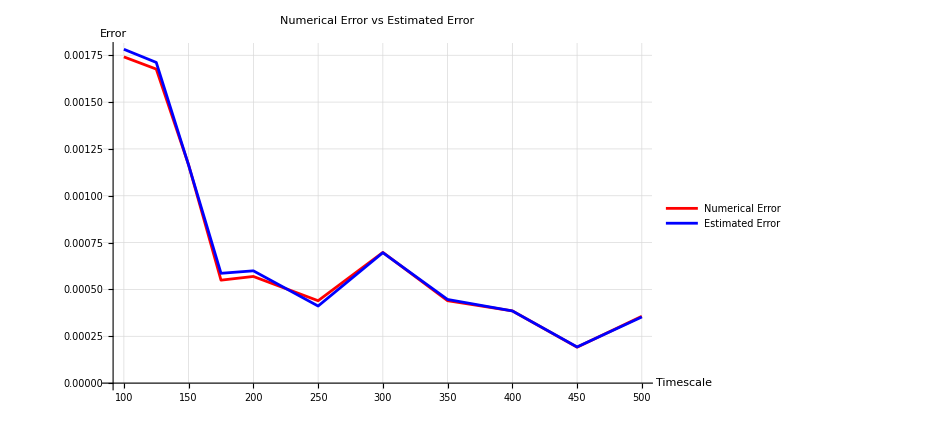

```mathematica
data={{100,0.00174119,0.00178187},{125,0.00167612,0.00171166},{150,0.0011642,0.00116305},{175,0.000549537,0.000586142},{200,0.000569245,0.000599354},{250,0.000439756,0.00041137},{300,0.000697584,0.000696216},{350,0.000439762,0.00044649},{400,0.000385479,0.000385278},{450,0.000191735,0.000193019}, {500, 0.000356746, 0.000352978}}

timescale=data[[All,1]];
numericalError=data[[All,2]];
estimatedError=data[[All,3]];

ListLinePlot[{Transpose[{timescale,numericalError}],Transpose[{timescale,estimatedError}]},PlotLegends->{"Numerical Error","Estimated Error"},PlotStyle->{Red,Blue},AxesLabel->{"Timescale","Error"},PlotLabel->"Numerical Error vs Estimated Error",GridLines->Automatic,ImageSize->Large]
```

{{0.366717,0.029274},{0.722842,0.0545852},{4.25965,0.151515},{7.12549,0.136054},{10.7549,0.612245},{15.0725,0.806127},{18.5316,0.887469},{22.2593,0.276727},{26.3563,1.19169},{29.3945,1.31105},{33.5774,1.35952},{37.7878,1.49343},{40.6137,1.51892},{44.9208,1.72911},{48.5584,1.40525},{52.042,1.92044},{56.209,2.06044},{67.0332,2.49307},{71.3351,2.65215},{74.8884,2.36686},{82.7106,2.60973},{89.7289,3.27869},{96.9641,3.53261},{104.784,3.83993},{104.784,3.83993},{112.41,3.37079},{116.043,3.68775},{119.297,2.66529},{123.297,3.91088},{127.558,4.13726},{131.255,3.42794},{142.09,4.28913},{150.238,4.54545},{156.671,4.96231},{168.181,1.51894},{175.686,5.06236},{187.535,2.53293},{206.256,2.47258},{224.206,6.75676},{235.643,7.40828},{261.989,8.13953},{280.512,8.78776},{299.604,7.82779},{336.799,9.86842}}

{{0.366717,0.029274},{0.722842,0.0545852},{4.25965,0.151515},{7.12549,0.136054},{10.7549,0.612245},{15.0725,0.806127},{18.5316,0.887469},{22.2593,0.276727},{26.3563,1.19169},{29.3945,1.31105},{33.5774,1.35952},{37.7878,1.49343},{40.6137,1.51892},{44.9208,1.72911},{48.5584,1.40525},{52.042,1.92044},{56.209,2.06044},{67.0332,2.49307},{71.3351,2.65215},{74.8884,2.36686},{82.7106,2.60973},{89.7289,3.27869},{96.9641,3.53261},{104.784,3.83993},{104.784,3.83993},{112.41,3.37079},{116.043,3.68775},{119.297,2.66529},{123.297,3.91088},{127.558,4.13726},{131.255,3.42794},{142.09,4.28913},{150.238,4.54545},{156.671,4.96231}}

{{224.206,6.75676},{235.643,7.40828},{261.989,8.13953},{280.512,8.78776},{299.604,7.82779},{336.799,9.86842}}

{a→0.0000140411,b→0.0220373,c→0.495716}

0.495716+0.0220373 x+0.0000140411 x^2

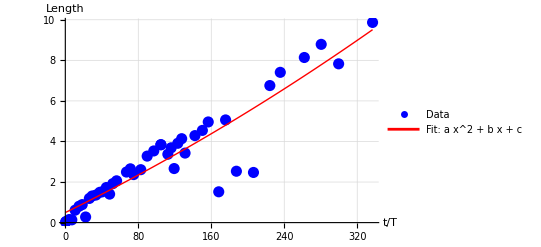

{a→-0.000062586,b→0.0386498,c→0.0473643}

0.0473643+0.0386498 x-0.000062586 x^2

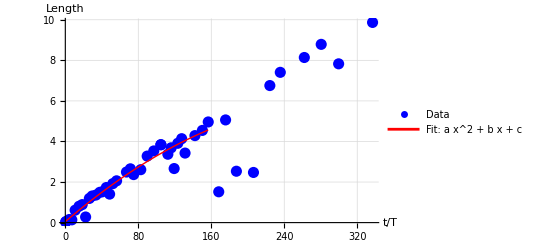

{a→0.0000105366,b→0.017212,c→2.62904}

2.62904+0.017212 x+0.0000105366 x^2

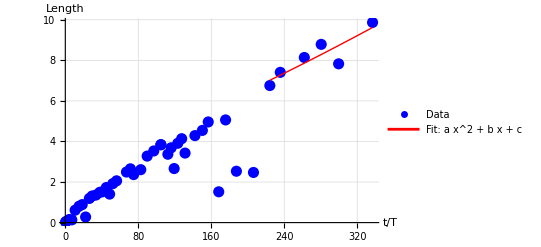

```mathematica
data = {{0.366717,0.02927400468},{0.722842,0.05458515284},{4.25965,0.1515151515},{7.12549,0.1360544218},{10.7549,0.612244898},{15.0725,0.8061265619},{18.5316,0.8874689386},{22.2593,0.2767272392},{26.3563,1.191692203},{29.3945,1.311045559},{33.5774,1.359516616},{37.7878,1.493428913},{40.6137,1.518917426},{44.9208,1.729106628},{48.5584,1.405253486},{52.042,1.920438957},{56.209,2.06043956},{67.0332,2.493074792},{71.3351,2.652149637},{74.8884,2.366863905},{82.7106,2.609727165},{89.7289,3.278688525},{96.9641,3.532608696},{104.784,3.839929784},{104.784,3.839929784},{112.41,3.370786517},{116.043,3.687754277},{119.297,2.6652896},{123.297,3.910879355},{127.558,4.137259674},{131.255,3.427944604},{142.09,4.289132692},{150.238,4.545454545},{156.671,4.962310073},{168.181,1.51893607},{175.686,5.062364016},{187.535,2.532928065},{206.256,2.472576875},{224.206,6.756756757},{235.643,7.408278457},{261.989,8.139534884},{280.512,8.787758067},{299.604,7.82778865},{336.799,9.868421053}}

data2 = {{0.366717,0.02927400468},{0.722842,0.05458515284},{4.25965,0.1515151515},{7.12549,0.1360544218},{10.7549,0.612244898},{15.0725,0.8061265619},{18.5316,0.8874689386},{22.2593,0.2767272392},{26.3563,1.191692203},{29.3945,1.311045559},{33.5774,1.359516616},{37.7878,1.493428913},{40.6137,1.518917426},{44.9208,1.729106628},{48.5584,1.405253486},{52.042,1.920438957},{56.209,2.06043956},{67.0332,2.493074792},{71.3351,2.652149637},{74.8884,2.366863905},{82.7106,2.609727165},{89.7289,3.278688525},{96.9641,3.532608696},{104.784,3.839929784},{104.784,3.839929784},{112.41,3.370786517},{116.043,3.687754277},{119.297,2.6652896},{123.297,3.910879355},{127.558,4.137259674},{131.255,3.427944604},{142.09,4.289132692},{150.238,4.545454545},{156.671,4.962310073}}

data3 = {{224.206,6.756756757},{235.643,7.408278457},{261.989,8.139534884},{280.512,8.787758067},{299.604,7.82778865},{336.799,9.868421053}}

fit=FindFit[data,a*x^2+b*x+c,{a,b,c},x]

fittedModel[x_]=a*x^2+b*x+c/. fit

Show[ListPlot[data,PlotStyle->{Blue,PointSize[0.02]},AxesLabel->{"t/T","Length"},PlotLegends->{"Data"}],Plot[fittedModel[x],{x,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->{Red,Thick},PlotLegends->{"Fit: a x^2 + b x + c"}],PlotRange->All,GridLines->Automatic]

fit2=FindFit[data2,a*x^2+b*x+c,{a,b,c},x]

fittedModel[x_]=a*x^2+b*x+c/. fit2

Show[ListPlot[data,PlotStyle->{Blue,PointSize[0.02]},AxesLabel->{"t/T","Length"},PlotLegends->{"Data"}],Plot[fittedModel[x],{x,Min[data2[[All,1]]],Max[data2[[All,1]]]},PlotStyle->{Red,Thick},PlotLegends->{"Fit: a x^2 + b x + c"}],PlotRange->All,GridLines->Automatic]

fit3=FindFit[data3,a*x^2+b*x+c,{a,b,c},x]

fittedModel[x_]=a*x^2+b*x+c/. fit3

Show[ListPlot[data,PlotStyle->{Blue,PointSize[0.02]},AxesLabel->{"Length","t/T"},PlotLegends->{"Data"}],Plot[fittedModel[x],{x,Min[data3[[All,1]]],Max[data3[[All,1]]]},PlotStyle->{Red,Thick},PlotLegends->{"Fit: a x^2 + b x + c"}],PlotRange->All,GridLines->Automatic]
```

{{-0.978011,0.442537,-1.13173,-0.885678},{0.442537,-0.888185,-0.238622,0.40392},{-1.13173,-0.238622,1.04262,-0.563516},{-0.885678,0.40392,-0.563516,0.552724}}

{{0.0482198,0.593326,-0.64427,0.680961},{0.593326,-0.00816359,-0.186093,-0.463839},{-0.64427,-0.186093,0.800334,0.700095},{0.680961,-0.463839,0.700095,0.545787}}

Numerical Errors Table for endTime = 305

Tscales | Numerical Errors
1 | 0.73214
2 | 0.789661
3 | 0.762129
4 | 0.834062
5 | 0.563358
6 | 0.978887
7 | 0.806603
8 | 0.342118
9 | 0.463472
10 | 0.205248
11 | 0.886594
12 | 0.540113
13 | 0.0920834
14 | 0.193956
15 | 0.0583839
16 | 0.170169
17 | 0.144222
18 | 0.43053
19 | 0.0555801
20 | 0.382045
21 | 0.105129
22 | 0.0123976
23 | 0.0521134
24 | 0.0900156
25 | 0.0595037
26 | 0.0641871
27 | 0.0886882
28 | 0.0321973
29 | 0.0140749
30 | 0.0188402
31 | 0.0154308
32 | 0.0255073
33 | 0.0417316
34 | 0.0162678
35 | 0.0391237
36 | 0.0139768
37 | 0.00821754
38 | 0.00990682
39 | 0.00720157
40 | 0.00605593
41 | 0.0066253
42 | 0.017766
43 | 0.00325013
44 | 0.00784013
45 | 0.00338826
46 | 0.00340387
47 | 0.00401389
48 | 0.00376855
49 | 0.00340303
50 | 0.00174655

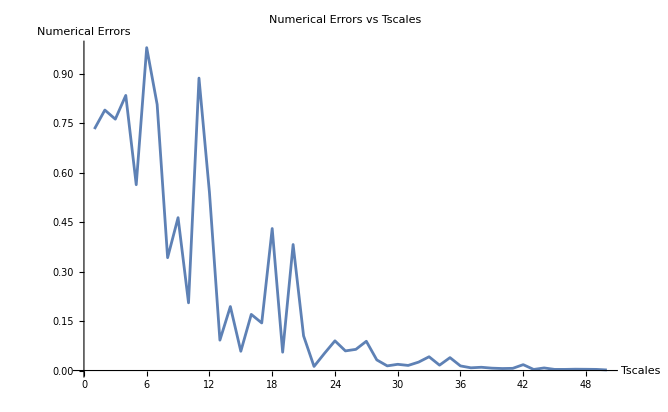

New Errors Table for endTime = 305

Interval | New Errors
21. | 0.105129
21.05 | 0.0945985
21.1 | 0.407404
21.15 | 0.145248
21.2 | 0.11301
21.25 | 0.385821
21.3 | 0.128625
21.35 | 0.117426
21.4 | 0.325393
21.45 | 0.106533
21.5 | 0.104785
21.55 | 0.181464
21.6 | 0.111837
21.65 | 0.0625538
21.7 | 0.107111
21.75 | 0.0944038
21.8 | 0.0602297
21.85 | 0.0505077
21.9 | 0.0749925
21.95 | 0.0427988
22. | 0.0123976
22.05 | 0.0595666
22.1 | 0.0606413
22.15 | 0.05477
22.2 | 0.152606
22.25 | 0.0880775
22.3 | 0.0632011
22.35 | 0.233516
22.4 | 0.0883247
22.45 | 0.087146
22.5 | 0.288594
22.55 | 0.121481
22.6 | 0.112665
22.65 | 0.291424
22.7 | 0.115664
22.75 | 0.0945585
22.8 | 0.227911
22.85 | 0.0532537
22.9 | 0.0687922
22.95 | 0.141666
23. | 0.0521134
23.05 | 0.0828846
23.1 | 0.096458
23.15 | 0.0529454
23.2 | 0.0479514
23.25 | 0.0197354
23.3 | 0.0435631
23.35 | 0.0234522
23.4 | 0.0203961
23.45 | 0.0435173
23.5 | 0.0451496
23.55 | 0.038689
23.6 | 0.0906199
23.65 | 0.0708169
23.7 | 0.0679989
23.75 | 0.149525
23.8 | 0.0712794
23.85 | 0.09115
23.9 | 0.187401
23.95 | 0.088213
24. | 0.0900156
24.05 | 0.206529
24.1 | 0.0720954
24.15 | 0.0648721
24.2 | 0.181111
24.25 | 0.0353956
24.3 | 0.0686818
24.35 | 0.126302
24.4 | 0.0172348
24.45 | 0.0734775
24.5 | 0.0699581
24.55 | 0.0216507
24.6 | 0.0490634
24.65 | 0.0100665
24.7 | 0.0232794
24.75 | 0.0349894
24.8 | 0.0179827
24.85 | 0.019213
24.9 | 0.0316361
24.95 | 0.0489013
25. | 0.0595037
25.05 | 0.0427714
25.1 | 0.0594049
25.15 | 0.0962282
25.2 | 0.0506348
25.25 | 0.0811335
25.3 | 0.123035
25.35 | 0.0578939
25.4 | 0.066517
25.45 | 0.157911
25.5 | 0.0507735
25.55 | 0.0471806
25.6 | 0.133036
25.65 | 0.0304129
25.7 | 0.0466478
25.75 | 0.102434
25.8 | 0.0124083
25.85 | 0.0622437
25.9 | 0.0342478
25.95 | 0.0106235
26. | 0.0641871
26.05 | 0.00370117
26.1 | 0.015036
26.15 | 0.0569167
26.2 | 0.0177578
26.25 | 0.0199701
26.3 | 0.0319998
26.35 | 0.0408405
26.4 | 0.0433205
26.45 | 0.020766
26.5 | 0.0471919
26.55 | 0.0566866
26.6 | 0.0416028
26.65 | 0.0618236
26.7 | 0.0799383
26.75 | 0.0389023
26.8 | 0.0527336
26.85 | 0.101079
26.9 | 0.0464847
26.95 | 0.0277532
27. | 0.0886882

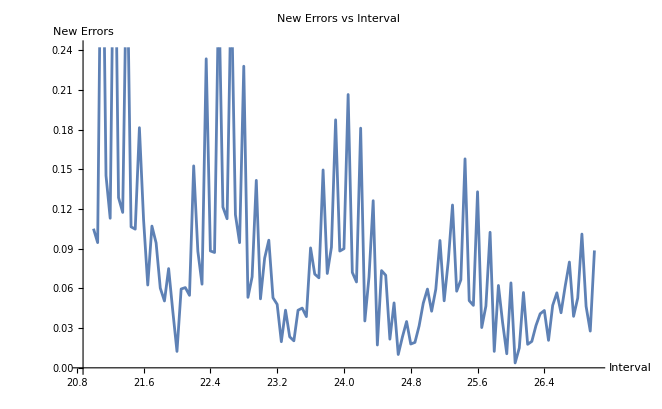

Timescale for endTime 305: 26.85

Numerical Errors Table for endTime = 310

Tscales | Numerical Errors
1 | 0.94484
2 | 0.608728
3 | 0.583308
4 | 0.700458
5 | 0.708514
6 | 0.972275
7 | 0.874801
8 | 0.343311
9 | 0.456846
10 | 0.167969
11 | 0.911178
12 | 0.512548
13 | 0.0648428
14 | 0.197412
15 | 0.0520298
16 | 0.17723
17 | 0.142875
18 | 0.418006
19 | 0.0517085
20 | 0.381833
21 | 0.120556
22 | 0.0118122
23 | 0.0509831
24 | 0.0919566
25 | 0.0545543
26 | 0.0753221
27 | 0.0981498
28 | 0.0296612
29 | 0.016308
30 | 0.0166022
31 | 0.0159815
32 | 0.0184241
33 | 0.0424225
34 | 0.0182758
35 | 0.032803
36 | 0.0136892
37 | 0.0152677
38 | 0.0107586
39 | 0.00645273
40 | 0.012586
41 | 0.00946515
42 | 0.0152565
43 | 0.00586208
44 | 0.0106125
45 | 0.00940681
46 | 0.00503552
47 | 0.00406327
48 | 0.00636105
49 | 0.00204964
50 | 0.00748756

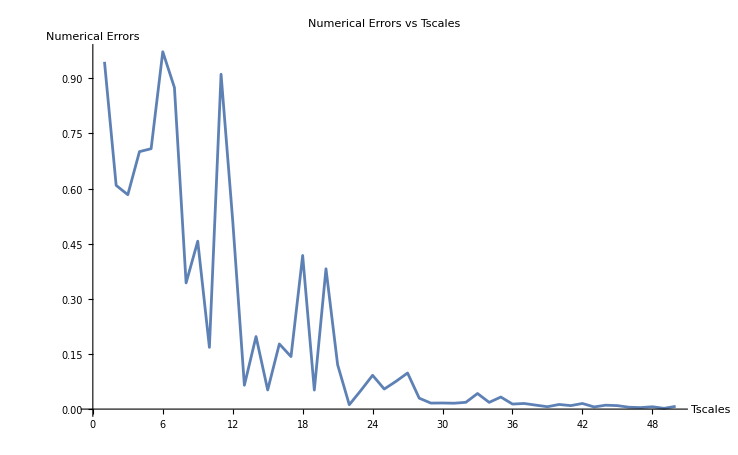

New Errors Table for endTime = 310

Interval | New Errors
21. | 0.120556
21.05 | 0.100566
21.1 | 0.400118
21.15 | 0.141979
21.2 | 0.122686
21.25 | 0.39008
21.3 | 0.127795
21.35 | 0.116581
21.4 | 0.324684
21.45 | 0.11075
21.5 | 0.109291
21.55 | 0.192617
21.6 | 0.110638
21.65 | 0.0701132
21.7 | 0.113476
21.75 | 0.0951689
21.8 | 0.0588827
21.85 | 0.0587362
21.9 | 0.0718038
21.95 | 0.0401996
22. | 0.0118122
22.05 | 0.0524949
22.1 | 0.0637879
22.15 | 0.0547521
22.2 | 0.151588
22.25 | 0.0894186
22.3 | 0.0635208
22.35 | 0.220593
22.4 | 0.100938
22.45 | 0.100023
22.5 | 0.289837
22.55 | 0.115992
22.6 | 0.115939
22.65 | 0.291029
22.7 | 0.117548
22.75 | 0.0973255
22.8 | 0.230856
22.85 | 0.0454637
22.9 | 0.0803927
22.95 | 0.153158
23. | 0.0509831
23.05 | 0.0890466
23.1 | 0.0998566
23.15 | 0.0539548
23.2 | 0.052709
23.25 | 0.0294512
23.3 | 0.0362967
23.35 | 0.0282755
23.4 | 0.025834
23.45 | 0.0388593
23.5 | 0.0485069
23.55 | 0.0407098
23.6 | 0.0869152
23.65 | 0.0771035
23.7 | 0.0767259
23.75 | 0.138791
23.8 | 0.0784277
23.85 | 0.100563
23.9 | 0.189703
23.95 | 0.0858011
24. | 0.0919566
24.05 | 0.203394
24.1 | 0.0702776
24.15 | 0.074674
24.2 | 0.188979
24.25 | 0.0242374
24.3 | 0.0798406
24.35 | 0.13375
24.4 | 0.0174014
24.45 | 0.0758331
24.5 | 0.0736812
24.55 | 0.0252375
24.6 | 0.0563168
24.65 | 0.0153867
24.7 | 0.0158418
24.75 | 0.0442595
24.8 | 0.0257814
24.85 | 0.0143581
24.9 | 0.0360517
24.95 | 0.0524802
25. | 0.0545543
25.05 | 0.0517754
25.1 | 0.0694715
25.15 | 0.0872231
25.2 | 0.0535685
25.25 | 0.0860915
25.3 | 0.124083
25.35 | 0.058667
25.4 | 0.07125
25.45 | 0.156225
25.5 | 0.0447595
25.55 | 0.0581507
25.6 | 0.144005
25.65 | 0.0244001
25.7 | 0.0531968
25.75 | 0.105151
25.8 | 0.0138776
25.85 | 0.0644042
25.9 | 0.0411344
25.95 | 0.0192288
26. | 0.0753221
26.05 | 0.00978322
26.1 | 0.0105708
26.15 | 0.0600549
26.2 | 0.022799
26.25 | 0.0184146
26.3 | 0.0355374
26.35 | 0.0450148
26.4 | 0.0393492
26.45 | 0.0285293
26.5 | 0.0572322
26.55 | 0.0494187
26.6 | 0.0418054
26.65 | 0.0641892
26.7 | 0.0798111
26.75 | 0.0402486
26.8 | 0.0593078
26.85 | 0.102143
26.9 | 0.0384126
26.95 | 0.0343475
27. | 0.0981498

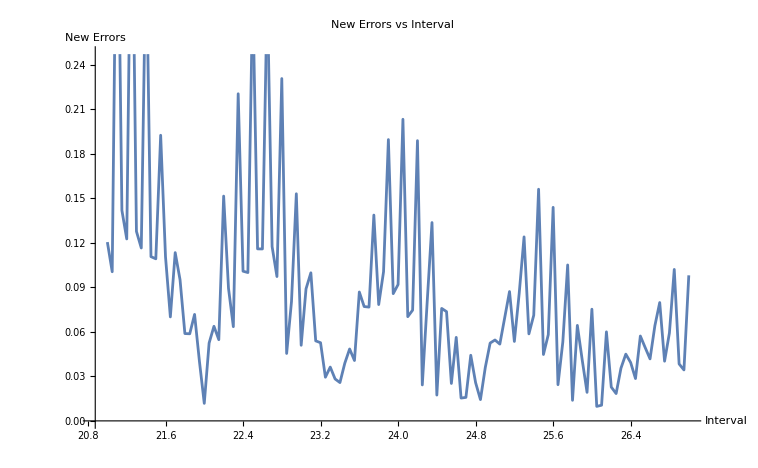

Timescale for endTime 310: 26.85

Numerical Errors Table for endTime = 315

Tscales | Numerical Errors
1 | 0.943827
2 | 0.684432
3 | 0.494744
4 | 0.58366
5 | 0.540081
6 | 0.980618
7 | 0.969561
8 | 0.403877
9 | 0.611003
10 | 0.240522
11 | 0.883137
12 | 0.496978
13 | 0.0847483
14 | 0.237314
15 | 0.0366307
16 | 0.168237
17 | 0.169431
18 | 0.435051
19 | 0.0464854
20 | 0.395286
21 | 0.103273
22 | 0.00892581
23 | 0.0432672
24 | 0.0761831
25 | 0.0607105
26 | 0.0698464
27 | 0.0877216
28 | 0.0314576
29 | 0.0124793
30 | 0.0163206
31 | 0.0177699
32 | 0.0213111
33 | 0.0362641
34 | 0.0126798
35 | 0.0369924
36 | 0.0130228
37 | 0.0114817
38 | 0.00841249
39 | 0.00669619
40 | 0.00756232
41 | 0.00783678
42 | 0.0190118
43 | 0.0016896
44 | 0.00816104
45 | 0.00653451
46 | 0.00294833
47 | 0.00335212
48 | 0.00460258
49 | 0.00441077
50 | 0.00405452

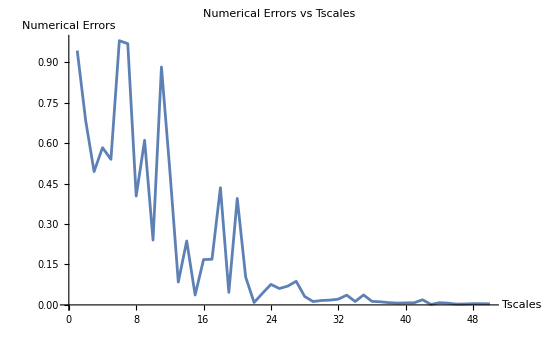

New Errors Table for endTime = 315

Interval | New Errors
21. | 0.103273
21.05 | 0.095302
21.1 | 0.414609
21.15 | 0.131683
21.2 | 0.115869
21.25 | 0.39929
21.3 | 0.121243
21.35 | 0.120206
21.4 | 0.329991
21.45 | 0.0973436
21.5 | 0.118748
21.55 | 0.197842
21.6 | 0.100889
21.65 | 0.0786365
21.7 | 0.119804
21.75 | 0.0951413
21.8 | 0.0572214
21.85 | 0.0622131
21.9 | 0.0771198
21.95 | 0.0324718
22. | 0.00892581
22.05 | 0.0617832
22.1 | 0.0548671
22.15 | 0.0475996
22.2 | 0.163051
22.25 | 0.0770876
22.3 | 0.0513258
22.35 | 0.231078
22.4 | 0.091342
22.45 | 0.0852767
22.5 | 0.295365
22.55 | 0.115149
22.6 | 0.101533
22.65 | 0.292844
22.7 | 0.122066
22.75 | 0.0904276
22.8 | 0.231049
22.85 | 0.0453087
22.9 | 0.0822298
22.95 | 0.154407
23. | 0.0432672
23.05 | 0.0919875
23.1 | 0.100841
23.15 | 0.0520359
23.2 | 0.0533707
23.25 | 0.0292968
23.3 | 0.0370289
23.35 | 0.026348
23.4 | 0.0221387
23.45 | 0.0431457
23.5 | 0.0424627
23.55 | 0.0332267
23.6 | 0.0941332
23.65 | 0.0690201
23.7 | 0.0654895
23.75 | 0.144824
23.8 | 0.0737697
23.85 | 0.0856208
23.9 | 0.192611
23.95 | 0.0904225
24. | 0.0761831
24.05 | 0.202402
24.1 | 0.078959
24.15 | 0.0635809
24.2 | 0.185293
24.25 | 0.0326555
24.3 | 0.0742962
24.35 | 0.128102
24.4 | 0.00917444
24.45 | 0.0716007
24.5 | 0.0677736
24.55 | 0.0229975
24.6 | 0.053454
24.65 | 0.00969816
24.7 | 0.0155106
24.75 | 0.0436233
24.8 | 0.0249403
24.85 | 0.0165199
24.9 | 0.0346207
24.95 | 0.0492618
25. | 0.0607105
25.05 | 0.0462941
25.1 | 0.0612516
25.15 | 0.094281
25.2 | 0.0516586
25.25 | 0.0755151
25.3 | 0.126073
25.35 | 0.0618251
25.4 | 0.0613615
25.45 | 0.152453
25.5 | 0.0537792
25.55 | 0.0481495
25.6 | 0.135624
25.65 | 0.0340473
25.7 | 0.0436203
25.75 | 0.094961
25.8 | 0.00550922
25.85 | 0.0572733
25.9 | 0.0325939
25.95 | 0.0127808
26. | 0.0698464
26.05 | 0.00853959
26.1 | 0.00809671
26.15 | 0.0583677
26.2 | 0.0225498
26.25 | 0.0190017
26.3 | 0.0359114
26.35 | 0.0416404
26.4 | 0.0453869
26.45 | 0.028339
26.5 | 0.0508881
26.55 | 0.0553305
26.6 | 0.0411625
26.65 | 0.0589494
26.7 | 0.0797802
26.75 | 0.0443439
26.8 | 0.0564013
26.85 | 0.0959781
26.9 | 0.047738
26.95 | 0.0282195
27. | 0.0877216

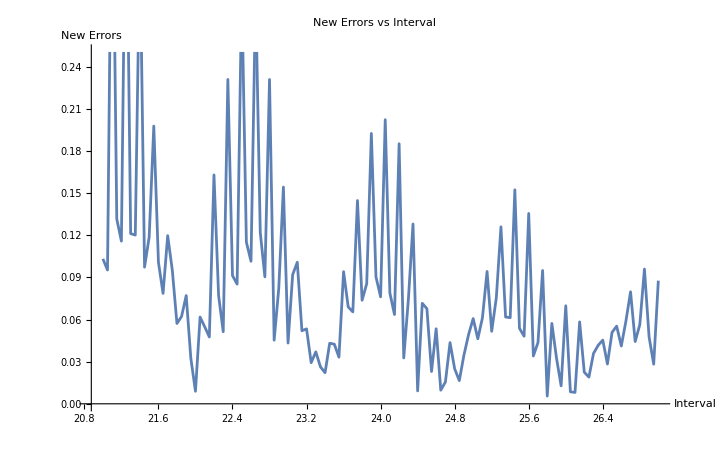

Timescale for endTime 315: 25.6

Numerical Errors Table for endTime = 320

Tscales | Numerical Errors
1 | 0.870954
2 | 0.789752
3 | 0.724797
4 | 0.694835
5 | 0.549846
6 | 0.968402
7 | 0.939494
8 | 0.481217
9 | 0.683954
10 | 0.274944
11 | 0.85982
12 | 0.485336
13 | 0.092089
14 | 0.231784
15 | 0.0284736
16 | 0.16883
17 | 0.160097
18 | 0.435891
19 | 0.049714
20 | 0.398779
21 | 0.104355
22 | 0.00524316
23 | 0.0440746
24 | 0.0744595
25 | 0.0592812
26 | 0.0736287
27 | 0.0878188
28 | 0.0323252
29 | 0.0146588
30 | 0.0170241
31 | 0.0192314
32 | 0.023789
33 | 0.0350536
34 | 0.0146955
35 | 0.0346841
36 | 0.0120388
37 | 0.00899553
38 | 0.00706136
39 | 0.00615401
40 | 0.00967289
41 | 0.00688867
42 | 0.0196887
43 | 0.00333908
44 | 0.00778251
45 | 0.00625079
46 | 0.00479852
47 | 0.00140519
48 | 0.00330707
49 | 0.00527879
50 | 0.00251687

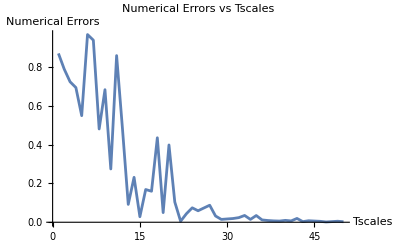

New Errors Table for endTime = 320

Interval | New Errors
21. | 0.104355
21.05 | 0.0915272
21.1 | 0.416002
21.15 | 0.126961
21.2 | 0.12146
21.25 | 0.402289
21.3 | 0.122355
21.35 | 0.115911
21.4 | 0.3285
21.45 | 0.0939838
21.5 | 0.121184
21.55 | 0.19787
21.6 | 0.10407
21.65 | 0.0768327
21.7 | 0.119425
21.75 | 0.0954139
21.8 | 0.0553468
21.85 | 0.0584747
21.9 | 0.0718085
21.95 | 0.0334486
22. | 0.00524316
22.05 | 0.064549
22.1 | 0.0540097
22.15 | 0.0489444
22.2 | 0.16157
22.25 | 0.0749685
22.3 | 0.047798
22.35 | 0.234485
22.4 | 0.0903447
22.45 | 0.086319
22.5 | 0.294201
22.55 | 0.113732
22.6 | 0.103885
22.65 | 0.296938
22.7 | 0.119767
22.75 | 0.0877108
22.8 | 0.226642
22.85 | 0.0464621
22.9 | 0.0834554
22.95 | 0.153995
23. | 0.0440746
23.05 | 0.0900771
23.1 | 0.100944
23.15 | 0.0488808
23.2 | 0.0544728
23.25 | 0.0284407
23.3 | 0.0364904
23.35 | 0.0293726
23.4 | 0.0217958
23.45 | 0.047255
23.5 | 0.0376483
23.55 | 0.0310557
23.6 | 0.0935299
23.65 | 0.0689082
23.7 | 0.0634111
23.75 | 0.148161
23.8 | 0.0712187
23.85 | 0.0896671
23.9 | 0.189168
23.95 | 0.0931322
24. | 0.0744595
24.05 | 0.20471
24.1 | 0.0763028
24.15 | 0.0631832
24.2 | 0.180499
24.25 | 0.0362471
24.3 | 0.0749223
24.35 | 0.129425
24.4 | 0.00949572
24.45 | 0.0694024
24.5 | 0.0663935
24.55 | 0.0192545
24.6 | 0.0570207
24.65 | 0.0140579
24.7 | 0.0178379
24.75 | 0.0421409
24.8 | 0.0260997
24.85 | 0.0190087
24.9 | 0.0319058
24.95 | 0.04523
25. | 0.0592812
25.05 | 0.0479941
25.1 | 0.0622482
25.15 | 0.0954144
25.2 | 0.0490732
25.25 | 0.0785731
25.3 | 0.121948
25.35 | 0.0665814
25.4 | 0.0592569
25.45 | 0.153261
25.5 | 0.0521178
25.55 | 0.0496056
25.6 | 0.132782
25.65 | 0.0373844
25.7 | 0.0439207
25.75 | 0.0977401
25.8 | 0.0063606
25.85 | 0.0557946
25.9 | 0.0303105
25.95 | 0.0120243
26. | 0.0736287
26.05 | 0.00628995
26.1 | 0.0100691
26.15 | 0.053932
26.2 | 0.0235316
26.25 | 0.0184976
26.3 | 0.0363164
26.35 | 0.038934
26.4 | 0.0425183
26.45 | 0.029049
26.5 | 0.0544868
26.55 | 0.0552468
26.6 | 0.0397936
26.65 | 0.0583765
26.7 | 0.0777275
26.75 | 0.0480717
26.8 | 0.0561142
26.85 | 0.0961541
26.9 | 0.0458549
26.95 | 0.0288273
27. | 0.0878188

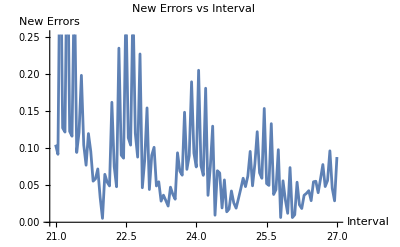

Timescale for endTime 320: 25.6

Numerical Errors Table for endTime = 325

Tscales | Numerical Errors
1 | 0.903795
2 | 0.55323
3 | 0.757547
4 | 0.68272
5 | 0.699802
6 | 0.882972
7 | 0.941477
8 | 0.542547
9 | 0.848247
10 | 0.206459
11 | 0.950142
12 | 0.608731
13 | 0.175222
14 | 0.0789219
15 | 0.145727
16 | 0.0688569
17 | 0.308729
18 | 0.531536
19 | 0.156533
20 | 0.369301
21 | 0.033009
22 | 0.106441
23 | 0.118285
24 | 0.157533
25 | 0.1424
26 | 0.107658
27 | 0.123597
28 | 0.0674018
29 | 0.0878374
30 | 0.0864455
31 | 0.0746981
32 | 0.0978275
33 | 0.0812009
34 | 0.0622001
35 | 0.0862685
36 | 0.0544247
37 | 0.0670986
38 | 0.0717303
39 | 0.069276
40 | 0.0677492
41 | 0.0561332
42 | 0.0512707
43 | 0.0558257
44 | 0.0569163
45 | 0.0593181
46 | 0.0559277
47 | 0.0525671
48 | 0.0500328
49 | 0.046853
50 | 0.0462503

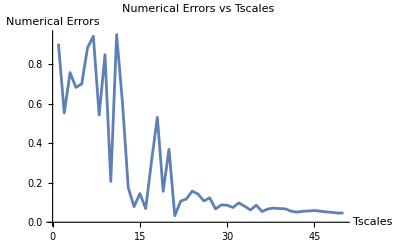

```mathematica
Needs["NumericalCalculus`"]

initialTime=0;
endTime=5;

dimension=4;
t1=1;
t2=1/Sqrt[2];
n=1000;
dt=0.01;
errorBound = 0.1;
Tscale[T_]:=T

generateGOEMatrix[n_Integer]:=Module[{matrix},matrix=Table[If[i==j,RandomVariate[NormalDistribution[0,1]],RandomVariate[NormalDistribution[0,1/Sqrt[2]]]],{i,n},{j,n}];
matrix=(matrix+Transpose[matrix])/2;matrix]

H[t_,T_]:=Tscale[T]*((Sin[t/t1]*2.1+Sin[t/t2])*Hinitial+(Cos[t/t1]*2.7+Cos[t/t2])*Hend)

groundState[t_,T_]:=Module[{eigenvalues,eigenvectors,minIndex},{eigenvalues,eigenvectors}=Eigensystem[H[t,T]];
minIndex=First[Ordering[Re[eigenvalues],1]];
Normalize[Re[eigenvectors[[minIndex]]]]]

generateGroundStates[dt_,T_]:=Module[{t,states,currentState,nextState,dotProduct},states={groundState[initialTime,T]};
currentState=groundState[initialTime,T];
For[t=initialTime,t<endTime,t+=dt,nextState=groundState[t+dt,T];
dotProduct=Re[Dot[currentState,nextState]];
If[dotProduct>=0,AppendTo[states,nextState],AppendTo[states,-nextState]];
currentState=Last[states];];
states]

state[t_,n_,T_]:=Module[{eigenvalues,eigenvectors,index},{eigenvalues,eigenvectors}=Eigensystem[H[t,T]];
index=Ordering[Re[eigenvalues],n+1][[n+1]];
Normalize[Re[eigenvectors[[index]]]]]

generateExcitedStates[dt_,n_,T_]:=Module[{t,states,currentState,nextState,dotProduct},states={state[initialTime,n,T]};
currentState=state[initialTime,n,T];
For[t=initialTime,t<endTime,t+=dt,nextState=state[t+dt,n,T];
dotProduct=Re[Dot[currentState,nextState]];
If[dotProduct>=0,AppendTo[states,nextState],AppendTo[states,-nextState]];
currentState=Last[states];];
states]

gap[t_,n_,T_]:=Module[{eigenvalues,sortedEigenvalues,smallestEigenvalue,nEigenvalue,difference},eigenvalues=Re[Eigenvalues[H[t,T]]];
sortedEigenvalues=Sort[eigenvalues];
smallestEigenvalue=sortedEigenvalues[[1]];
nEigenvalue=sortedEigenvalues[[n+1]];
difference=nEigenvalue-smallestEigenvalue;
difference]

omega[n_,T_]:=NIntegrate[gap[t,n,T]/Tscale[T],{t,initialTime,endTime}]

derivativeGroundState[t_?NumericQ,T_,h_:0.01]:=(groundState[t+h,T]-groundState[t-h,T]*(groundState[t+h,T].groundState[t-h,T]))/(2*h)

normDerivativeGroundState[t_,T_]:=Norm[derivativeGroundState[t,T]]

Hinitial={{-0.978011,0.442537,-1.13173,-0.885678},{0.442537,-0.888185,-0.238622,0.40392},{-1.13173,-0.238622,1.04262,-0.563516},{-0.885678,0.40392,-0.563516,0.552724}}

Hend={{0.0482198,0.593326,-0.64427,0.680961},{0.593326,-0.00816359,-0.186093,-0.463839},{-0.64427,-0.186093,0.800334,0.700095},{0.680961,-0.463839,0.700095,0.545787}}

calculateNumericalError[T_,endTime_]:=Module[{schrodingerEqu,initialCondition,sol,psiFunction,numericalError},schrodingerEqu=I D[psi[t],t]==H[t,T].psi[t];
initialCondition=psi[initialTime]==groundState[initialTime,T];
sol=NDSolve[{schrodingerEqu,initialCondition},psi,{t,initialTime,endTime}];
psiFunction=psi/. First[sol];
numericalError=Sqrt[Abs[1-Abs[groundState[endTime,T].psiFunction[endTime]]^2/Norm[psiFunction[endTime]]^2]];
numericalError]

findTimescaleWithNumericalError[endTime_]:=Module[{startT=1,endT=50,Tscales,numericalErrors,lastTransitionIndex=-1,newDt=0.05,interval,newErrors,result},Tscales=Range[startT,endT];
numericalErrors=Table[calculateNumericalError[T,endTime],{T,Tscales}];
(*Printing numericalErrors table*)Print["Numerical Errors Table for endTime = ",endTime];
Print[TableForm[Transpose[{Tscales,numericalErrors}],TableHeadings->{None,{"Tscales","Numerical Errors"}}]];
(*Plotting numericalErrors*)Print[ListLinePlot[Transpose[{Tscales,numericalErrors}],PlotLabel->"Numerical Errors vs Tscales", PlotRange -> {0, 0.2},AxesLabel->{"Tscales","Numerical Errors"}]];
Do[If[numericalErrors[[i]]<=errorBound&&(i==1||numericalErrors[[i-1]]>errorBound),lastTransitionIndex=i;],{i,Length[numericalErrors]}];
If[lastTransitionIndex==-1,Print["No transition in this interval for endTime = ",endTime];
Return[None]];
interval=Range[Tscales[[lastTransitionIndex-1]],Min[Tscales[[lastTransitionIndex+7]],endT],newDt];
newErrors=Table[{T,calculateNumericalError[T,endTime]},{T,interval}];
(*Printing newErrors table*)Print["New Errors Table for endTime = ",endTime];
Print[TableForm[newErrors,TableHeadings->{None,{"Interval","New Errors"}}]];
(*Plotting newErrors*)Print[ListLinePlot[newErrors,PlotLabel->"New Errors vs Interval",PlotRange -> {0, 0.2},AxesLabel->{"Interval","New Errors"}]];
result=None;
For[i=Length[newErrors],i>=1,i--,If[errorBound-newErrors[[i,2]]<0.000001,result=newErrors[[i,1]];
Break[];]];
If[result=!=None,Print["Timescale for endTime ",endTime,": ",result];
result,Print["No timescale found for endTime ",endTime];
None]]

results=Table[findTimescaleWithNumericalError[endTime],{endTime,305,400,5}];

results
```